# fresnel diffraction validity

P. Huft

The Fresnel approximation validity condition can be restated in terms of the NA of the beam or system considered, using ρ_max/z=tan(sin^-1(NA)).

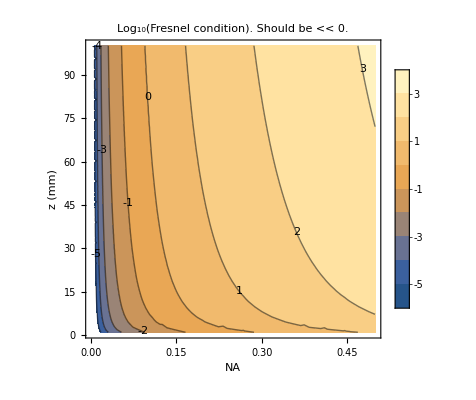

```mathematica
mm=1;
um=10^-3;
λ=1um;
condition=Tan[ArcSin[NA]]^4/(8λ/z);
ContourPlot[Log[10,condition],{NA,0,0.5},{z,1mm,100mm},PlotLegends->Automatic,FrameLabel->{"NA","z (mm)"},PlotLabel->"Log_10(Fresnel condition). Should be << 0.", ContourLabels->True]
```

Transformation from the object plane of the mask with aperture radius a to the Fourier plane after a lens of focal length f1.

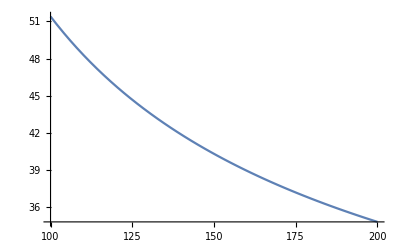

```mathematica
zf =((k/(8π))((a-b)^2)^2)^(1/3);
a = 0.1;
b = f1*3.8317/(k a);
k = 2π/(8.08*^-4);
Plot[f1/zf,{f1,100,200}]
```

Transformation from the Fourier plane filter of radius b to the image plane after a lens of focal length f2 = mag*f1.

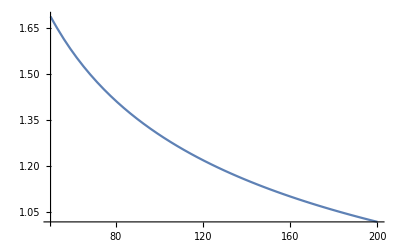

```mathematica
fov =  10^-2;
zf =((k/(8π))((b-fov)^2)^2)^(1/3);
a = 0.1;
k = 2π/(8.08*^-4);
b = f1*3.8317/(k a);
mag = 1/30;
Plot[(f1*mag)/zf,{f1,50,200}]
```

```mathematica
0.03*.100
```

0.003